```mathematica
(*This note deals with the problem on calculating edge states induced with SOC. Here we write the penetration length λ using Euler's formula, with respect ot ρ and θ. In the ContourPlot, since Det[M1] has both real and imaginary parts, we write the equation Det[M1]==0 seperately, and plot it with respect to k1 and energy ϵ.*)
```

```mathematica
M[t1_,t2_,t3_,k1_,E_,λ_]:={{E,-(t1+2ⅈ t3 ⅇ^(-ⅈ k1))-ⅈ t3 λ,-t2 ⅇ^(-ⅈ k1),-(t1-2ⅈ t3 ⅇ^(-ⅈ k1))-ⅈ t3/λ },{-(t1-2ⅈ t3 ⅇ^(ⅈ k1))+ⅈ t3/λ, E, -(t1+2ⅈ t3 ⅇ^(-ⅈ k1))-ⅈ t3/λ ,-t2 /λ },{-t2 ⅇ^(ⅈ k1),-(t1-2ⅈ t3 ⅇ^(ⅈ k1))+ⅈ t3 λ,E,-(t1+2ⅈ t3 ⅇ^(ⅈ k1))-ⅈ t3/λ },{-(t1+2ⅈ t3 ⅇ^(ⅈ k1))-ⅈ t3 λ,-t2 λ,-(t1-2ⅈ t3 ⅇ^(-ⅈ k1))+ⅈ t3 λ,E}};
ρ=0.1;
θ=π/6;
```

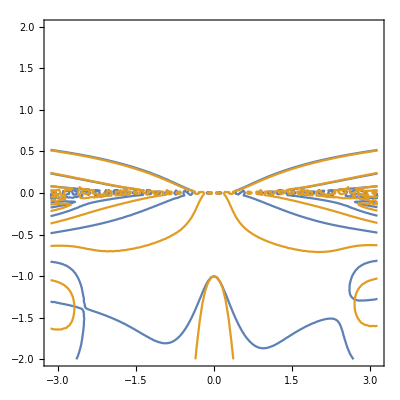

```mathematica
With[{t1=0.8,t2=1.0,t3=0.01,λ=ρ(Cos[θ]+Sin[θ]ⅈ)},M1=M[t1,t2,t3,k1,ϵ,λ]];
ContourPlot[{Re[Det[M1]]==0,Im[Det[M1]]==0},{k1,-π,π},{ϵ,-2,2}]
```

```mathematica
Solve[Re[Det[M1]]==0,k1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

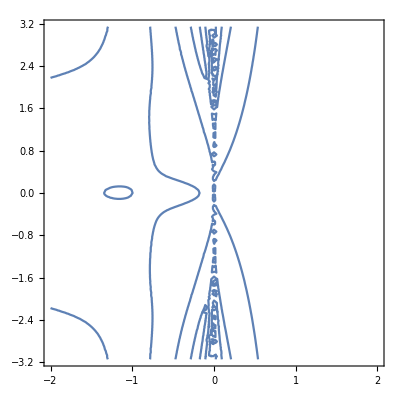

```mathematica
ContourPlot[Re[Det[M1]]==0,{ϵ,-2,2},{k1,-π,π}]
```

```mathematica
ContourPlot[Det[M1]==0,{ϵ,-2,2},{k1,-π,π}]
```